# Benford’s Law

Benford’s Law is an empirical law in statistics that states that the leading significant digit of numerical data in real life is likely to be small.

## Discovering Benford’s Law

In statistics, not a lot of attention is paid to the first digits of numbers. They seem so simple that it’s meaningless to study them.

Make a histogram of the first digits of the first n natural numbers with n ranging from 10000 to 100000:

```mathematica
Manipulate[Histogram[Array[IntegerDigits[#][[1]]&,n],9,"Probability"],{n,10000,100000,1000}]
```

The pattern may look unfamiliar, but it’s easily understandable. Obviously, random integers behave similarly.

Make a histogram of the first digits of 10000 random integers up to n with n ranging from 10000 to 100000:

```mathematica
Manipulate[Histogram[DeleteCases[Table[IntegerDigits[RandomInteger[n]][[1]],10000],0],9,"Probability"],{n,10000,100000,1000}]
```

This seems like a boring topic. Let’s take a look at some meaningful sequences, starting from the primes.

Make a histogram of the first digits of the first n primes with n ranging from 10000 to 100000:

```mathematica
Manipulate[Histogram[Array[IntegerDigits[Prime[#]][[1]]&,n],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&)],{n,10000,100000,1000}]
```

It seems that the first digit of primes is slightly more likely to be small, but the difference is nonobvious. But what about the Fibonacci numbers?

Make a histogram of the first digits of the first n Fibonacci numbers with n ranging from 1000 to 10000:

```mathematica
Manipulate[Histogram[Array[IntegerDigits[Fibonacci[#]][[1]]&,n],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&)],{n,1000,10000,100}]
```

Whoa, wait a sec. Why is this so stable and what is this weird pattern? Let’s try more, say factorials.

Make a histogram of the first digits of the first n factorials with n ranging from 100 to 1000:

```mathematica
Manipulate[Histogram[Array[IntegerDigits[#!][[1]]&,n],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&)],{n,100,1000,10}]
```

The same stable pattern shows again. This is getting interesting. What about powers of 2?

Make a histogram of the first digits of the first n powers of 2 with n ranging from 1000 to 10000:

```mathematica
Manipulate[Histogram[Array[IntegerDigits[2^#][[1]]&,n],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&)],{n,1000,10000,100}]
```

This is too good to be coincidence. And yet this is not the end of story. Now let’s move on to some data from real life, starting with the populations of countries.

Make a histogram of the first digits of the populations of all the countries in the world:

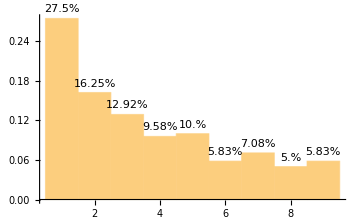

```mathematica
Histogram[IntegerDigits[QuantityMagnitude[#]][[1]]&/@EntityClass["Country","Countries"][EntityProperty["Country","Population"]],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&),ImageSize->Medium]
```

The distribution is generally similar. What about the total areas of countries?

Make a histogram of the first digits of the total areas of all the countries in the world in various units:

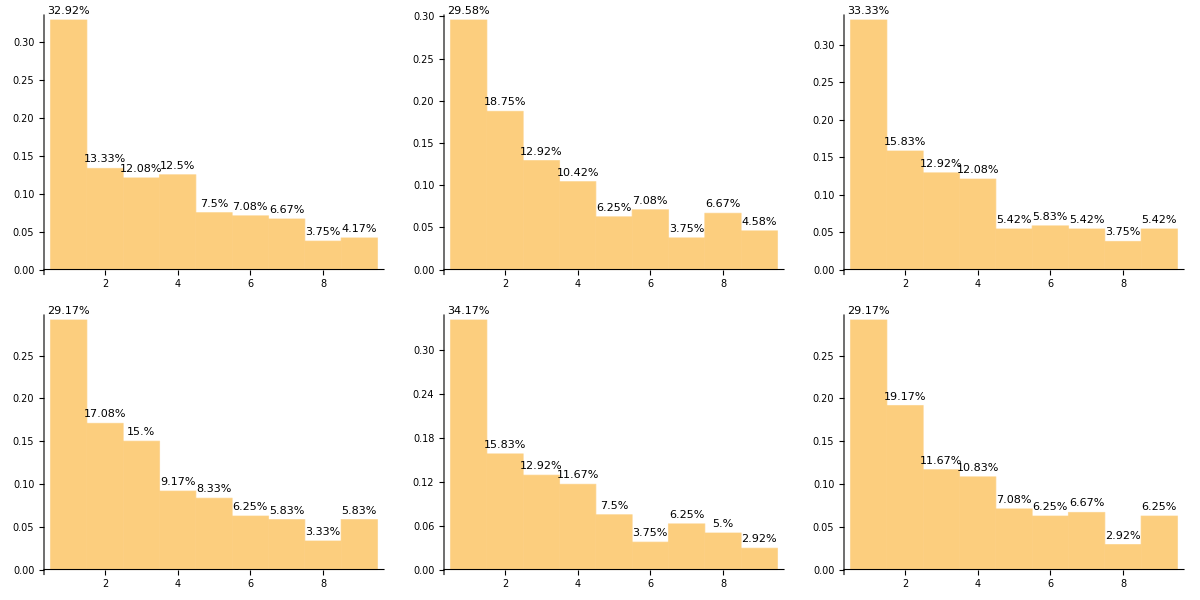

```mathematica
Partition[Table[Histogram[RealDigits[N[QuantityMagnitude[UnitConvert[#,u]]]][[1,1]]&/@EntityClass["Country","Countries"][EntityProperty["Country","Area"]],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&),ImageSize->Medium],{u,{"Inches Squared","Feet Squared","Miles Squared","Yards Squared","Leagues Squared","Kilometers Squared"}}],3]//Grid
```

Does this pattern apply to any set of data? Let’s take a look at the heights of the tallest structures in the world.

Make a histogram of the first digits of the heights of the top 1000 tallest structures in the world in various units:

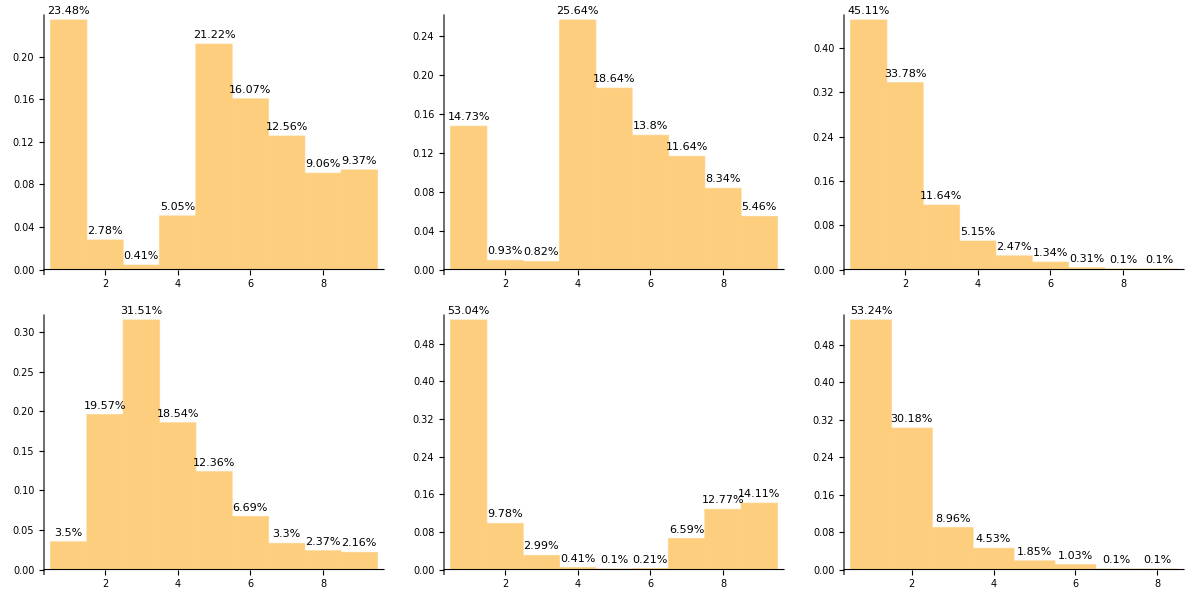

```mathematica
Partition[Table[Histogram[RealDigits[QuantityMagnitude[UnitConvert[#,u]]][[1,1]]&/@DeleteMissing[["Height"]],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&),ImageSize->Medium],{u,{"Inches","Feet","Yards","Leagues","Miles","Kilometers"}}],3]//Grid
```

Although the general trend holds in some histograms, most are quite divergent from the pattern that we saw above. The final example is the lengths of the longest rivers in the world.

Make a histogram of the first digits of the lengths of the top 1000 longest rivers in the world in various units:

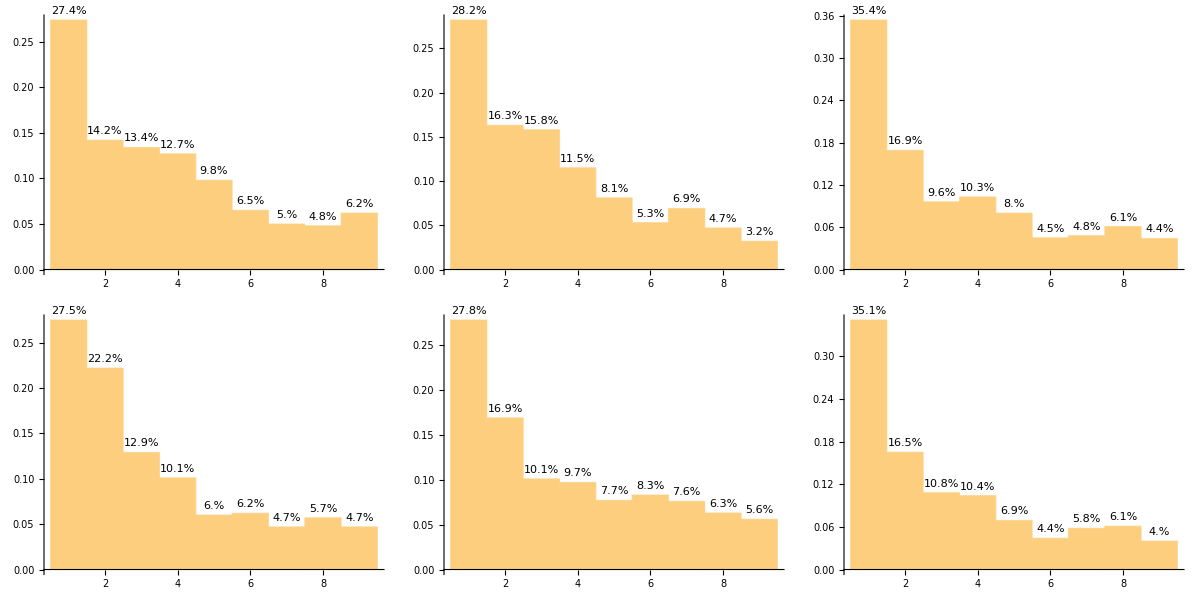

```mathematica
Partition[Table[Histogram[RealDigits[N[QuantityMagnitude[UnitConvert[#,u]]]][[1,1]]&/@["Length"],9,"Probability",LabelingFunction->(Placed[Row[{Round[100#,0.01],"%"}],Above]&),ImageSize->Medium],{u,{"Inches","Feet","Yards","Leagues","Miles","Kilometers"}}],3]//Grid
```

Curiously, the pattern seems to return. Is there a reason behind all this? The answer is Benford’s Law.

## Introducing Benford’s Law

The probability density function of Benford Distribution with base parameter 10:

```mathematica
Style[PDF[BenfordDistribution[10],x],30]
```

Piecewise[{{Log[1+1/x]/Log[10], 1≤x<10}, {0, True}}]

Plot a Benford Distribution:

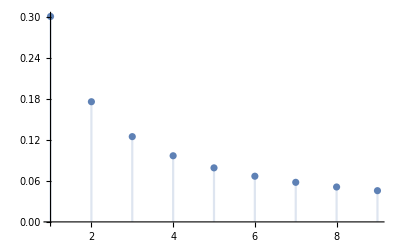

```mathematica
DiscretePlot[PDF[BenfordDistribution[10],x],{x,1,9}]
```

It’s amazing how well the sequences of Fibonacci numbers, factorials, and powers of 2 fit Benford Distribution.

Combine the plot of Benford Distribution and the histograms for the sequences of Fibonacci numbers, factorials, and powers of 2:

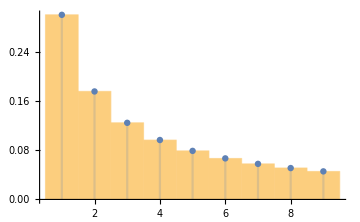
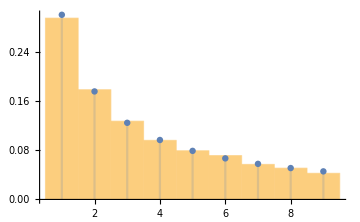
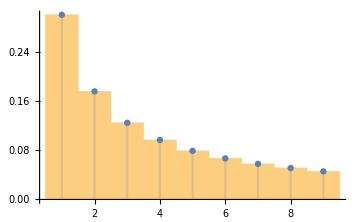

```mathematica
Show[#,%]&/@(Histogram[Table[IntegerDigits[#[i]][[1]],{i,10000}],9,"Probability",ImageSize->Medium]&/@{Fibonacci,Factorial,(2^#)&})//Row
```

Many sets of data from real life also show good fit.

Combine the plot of Benford Distribution with the histograms for populations, total areas, and lengths of rivers:

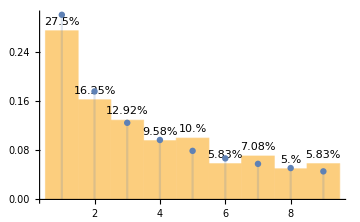
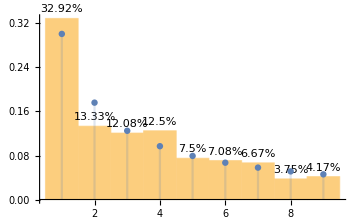
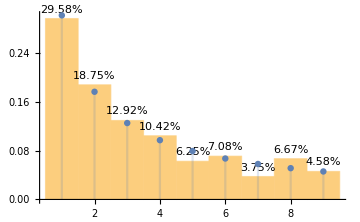
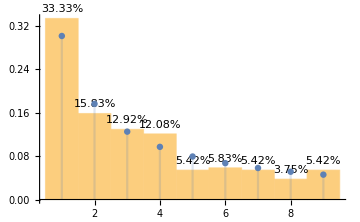
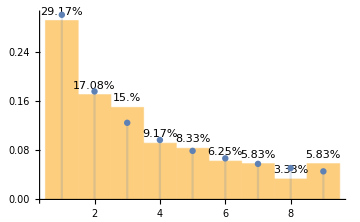
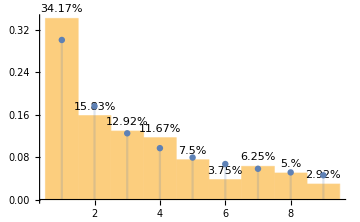
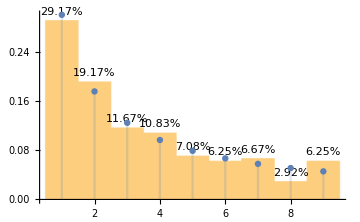
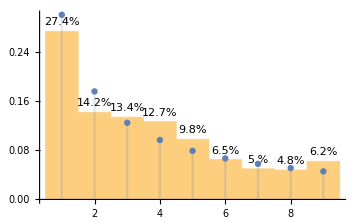
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
Partition[Show[#,%%]&/@Join[{%7},Flatten@@%8,Flatten@@%10],UpTo[3]]//Grid
```

As we’ve seen above, there are exceptions that fit rather poorly.

Combine the plot of Benford Distribution with the histograms for heights of structures:

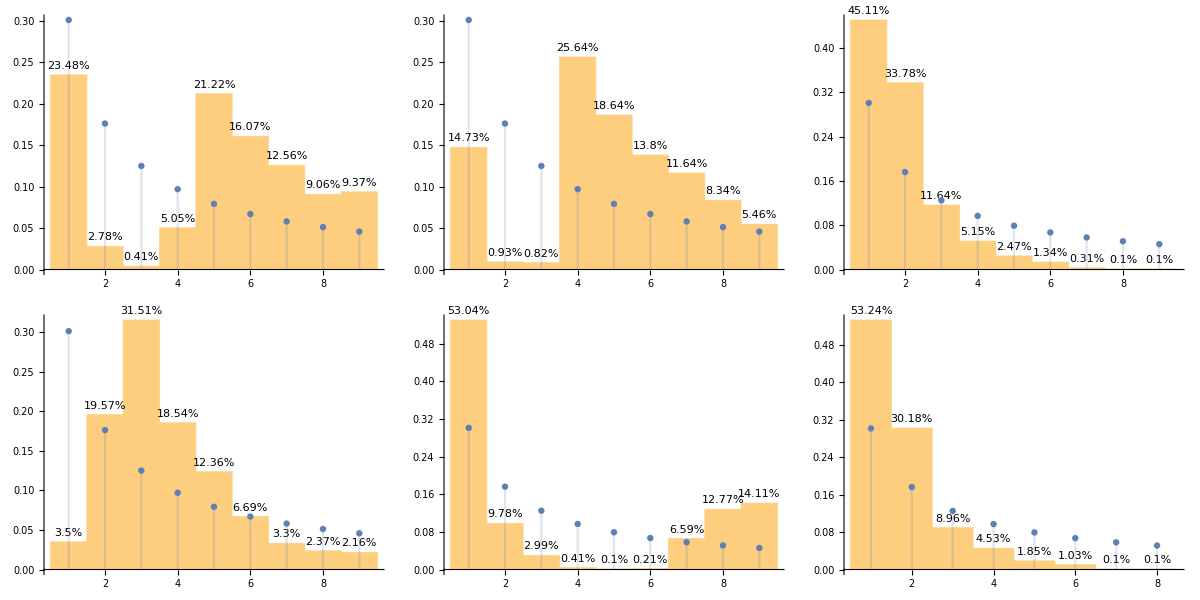

```mathematica
Partition[Show[#,%%%]&/@Flatten@@%9,3]//Grid
```

A natural question is: why and when does Benford’s Law apply? Here’s a simple explanation.

## Explaining Benford’s Law

For any number X, it has a scientific notation: X = r × 10^n, where 1 ≤ r < 10 and n ∈ ℤ, and log_10X = log_10(r × 10^n) = log_10r + n. Therefore, that the first digit of X is 1 is equivalent to that ⌊log_10X⌋ < log_102, which is approximately 0.301, and that the first digit of X is 9 is equivalent to that ⌊log_10X⌋ ≥ log_109, which is approximately 0.954, and 1 - 0.954 = 0.046. More generally, that the first digit of X is d is equivalent to that log_10d ≤ log_10X < log_10(d+1), and log_10(d+1) - log_10d = log_10(1 + 1/d), which is congruent with Benford’s Distribution.
So what happens if a set of data has a narrow distribution after taking log10?

Plot a normal distribution with standard deviation 1/3 and the regions that correspond to numbers whose first digits are 1 and 9:

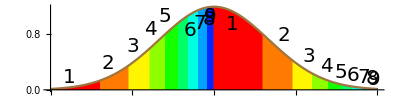

```mathematica
Plot[Labeled[PDF[NormalDistribution[1,1/3],x],Join[Array[Style[#,20]&,9],Array[Style[#,20]&,9]],Join[Log10[Range[9]*Range[2,10]]/2,Log10[Range[9]*Range[2,10]]/2+1]],{x,0,2},AspectRatio->1/4,ColorFunction->Function[{x,y},Hue[0.08(Floor[10^FractionalPart[x]]-1)]],ColorFunctionScaling->False,Filling->Axis,PlotPoints->1000,ImageSize->Full]
```

Since the data are very centralized and change rapidly in “blocks of 1”, they won’t obey Benford’s Law very well. On the other hand, what happens if a set of data has a broad distribution after taking log10?

Plot a normal distribution with standard deviation 2 and the regions that correspond to numbers whose first digits are 1 (red) and 9 (blue):

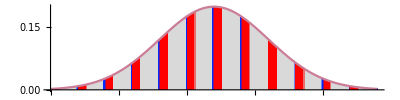

```mathematica
Plot[PDF[NormalDistribution[6,2],x],{x,0,12},AspectRatio->1/4,ColorFunction->Function[{x,y},If[FractionalPart[x]≤Log10[2],Hue[0],If[FractionalPart[x]≥Log10[9],Hue[0.64],LightGray]]],ColorFunctionScaling->False,Filling->Axis,PlotPoints->1000,ImageSize->Full]
```

Since the data are very flat in every “block of 1” and span several orders of magnitude rather uniformly, they will obey Benford’s Law very well.
This explains why the sequences of Fibonacci numbers, factorials, and powers of 2 obey Benford’s Law much better than the sequence of primes: the formers increase faster and therefore distribute more uniformly than the latter.

Plot the histograms of the sequences of Fibonacci numbers, factorials, powers of 2, and primes after taking log10:

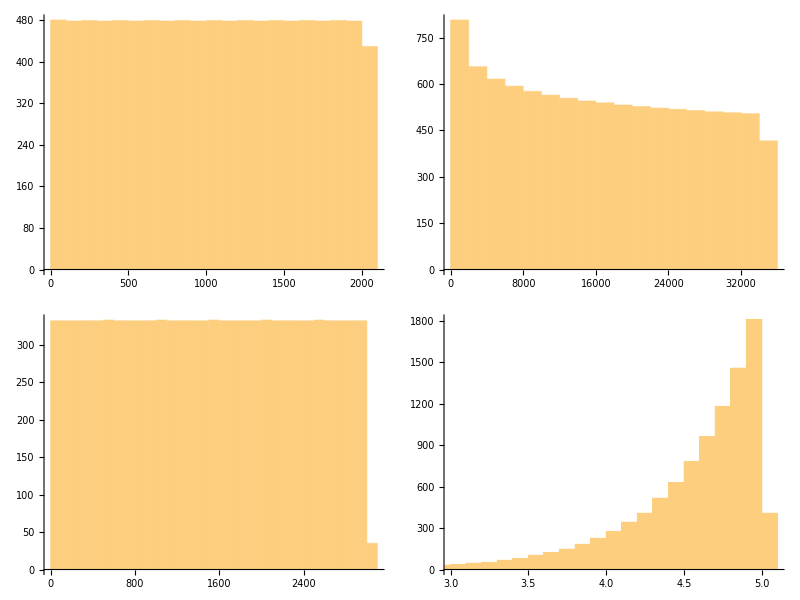

```mathematica
Partition[Histogram[Table[Log10[#[i]],{i,10000}],ImageSize->Medium]&/@{Fibonacci,Factorial,(2^#&),Prime},2]//Grid
```

Apparently, the first three histograms are very flat and uniform, while that of the prime sequence is unsymmetric and steep. The populations and total areas of countries are not as uniform, but they are rather symmetric and span several orders of magnitude.

Plot the histograms of the populations and total areas of countries after taking log10:

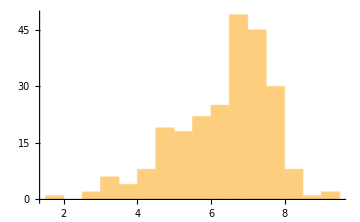
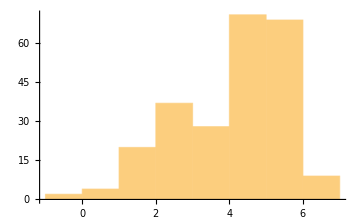

```mathematica
Histogram[Log10[QuantityMagnitude[EntityClass["Country","Countries"][#]]],ImageSize->Medium]&/@{EntityProperty["Country","Population"],EntityProperty["Country","Area"]}//Row
```

On the other hand, since we take only the top 1000 tallest structures and there are many “tallish” buildings, the distribution is very narrow and unsymmetric as it’s greatly skewed to the right. The lengths of rivers are better because there are much fewer long rivers than tall buildings and the top 1000 longest rivers already includes a wide range of them.

Plot the histogram of the heights of 1000 tallest structures and the lengths of 1000 longest rivers after taking log10:

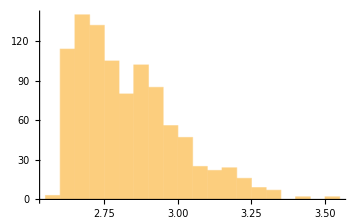
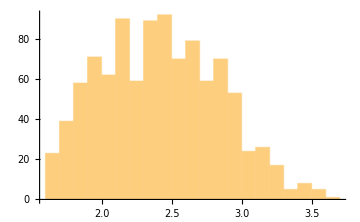

```mathematica
Histogram[Log10[QuantityMagnitude[#]],ImageSize->Medium]&/@{["Height"],["Length"]}//Row
```

And finally, back to our original example, we can see how random integers behave that way by comparing it to the log10 plot.

Plot the histogram of the first digits of 5000 random integers up to n with n ranging from 10000 to 100000 and the logarithms of the random integers with highlighted regions corresponding to integers whose first digits are 1 (red) and 9 (blue):

```mathematica
Manipulate[Row[{Histogram[DeleteCases[Table[IntegerDigits[RandomInteger[n]][[1]],5000],0],9,"Probability",ImageSize->500],Show[Histogram[Log10/@RandomInteger[n,5000],{0.1},"Probability",PlotRange->{{2.5,5},Automatic}],RegionPlot[FractionalPart[x]<Log10[2],{x,2.5,5},{y,0,0.25},PlotStyle->{Directive[Hue[0],Opacity[0.2]]},PlotPoints->30],RegionPlot[FractionalPart[x]>Log10[9],{x,2.5,5},{y,0,0.25},PlotStyle->{Directive[Hue[0.64],Opacity[0.2]]},PlotPoints->50],ImageSize->500]}],{n,10000,100000,1000}]
```

Further Explorations

A more general form of Benford’s Law: Zipf’s Law

Authorship information

Matthew Chen

Jun 19, 2017

yuanzhec@andrew.cmu.edu